# Analytic estimate of FCC-ee sensitivity for HNLs during Z-pole run (based on arXiv:2210.17110)

## General (pre)settings

### Computational settings

```mathematica
$PreRead=(#/.s_String/;StringMatchQ[s,NumberString]&&Precision@ToExpression@s==MachinePrecision:>s<>"`20."&);

$PerformanceGoal->"Quality";
```

```mathematica
$Assumptions={kinematics>0,pN>0,cprod>0,NZ>0,Brα>0,Uα2>0,IP>0,Y>0,l>0,d>0};
```

```mathematica
recursionen=5;
```

### Constants of Nature

```mathematica
cm=1/(1.98*10^(-14)*GeV);(*conversion cm to GeV*)
GF=1.16*10^(-5)/GeV^2; (*Fermi constant*)
mZ=90*GeV; (*Z boson mass*)
pb=1000*fb; (*femtobarn picobarn conversion*)
nb=1000*pb;
Brα=1/15; (*Z ->⋁_α OverBar[⋁_α]   branching ratio*)
a=11.9; (* numerical prefactor in Subscript[Γ, N] when all final state masses are negligible*)
cdec=1; (*to be set according to footnote 20 in the arXiv version or footnote 2 in the version published in PoS*)
cprod=1; (*to be set according to footnote 20 in the arXiv version or footnote 2 in the version published in PoS*)
```

```mathematica
GeV=1;(*for pure convenience*)
```

## User Specified Parameters

### General settings

```mathematica
Nobs=4; (*number of events one wants to see; the code will produce an "Nobs-event curve"*)
IP=2;(*number of interaction points*)
NZ=2.5*10^12;(*number of Z bosons at each IP*)
```

```mathematica
l0=0.04*cm;(*minimal displacement for which background-free assumption can be justified*)
```

```mathematica
cylinder=True;(*set to "False" if you want a spherical detector*)
If[cylinder,l1=1/2 (3/2)^(1/3) d^(2/3) l^(1/3),l1=l1spherical];
```

### Spherical detector

```mathematica
l1spherical=122*cm;(*radius of a hypothetical spherical detector, can be ignored if cylinder=True*)
```

### Cylindrical detector

```mathematica
(*l=11*100*cm;
d=2*100*4.5*cm;(*IDEA*)*)
```

```mathematica
l=8.6*100*cm;
d=2*100*5*cm;(*CLD*)
```

### Efficiencies

```mathematica
ϵαβ=BrFinalState*ϵαβDetector;
(*fraction of HNL decays that can be seen. Setting it BrFinalState=ϵαβDetector=1 means that HNL decays into all final states can be seen with 100% efficiency.*)

BrFinalState=1; (*If only specific final states are to be taken into account, set BrFinalState to the HNL decay branching ratio into the desired final state.*)

ϵαβDetector=1;(*ϵαβDetector permits to introduce an overall detector efficiency (independent of displacement, energy, angle...).*)
```

### HNL parameters

```mathematica
uα2=1;(*Uα^2/U^2*)
uβ2=1;(*Uβ^2/U^2*)
```

```mathematica
Mmin=5*GeV;(*minimal and maximal HNL mass. Should be somewhere between the masses of b-hadrons and the Z-boson mass*)
Mmax=80*GeV;
```

```mathematica
U2min=-12;(*Log10 of minimal and maximal U^2 to be plotted*)
U2max=-5;
```

```mathematica
cprod=1;(*set to 1 for Majorana and Dirac, and to 2 for pseudo-Dirac, cf. footnote 20 in the arXiv version or footnote 2 in the version published in PoS**)
cdec=1;(*set to 1 for Majorana and 1/2 for Dirac*)
```

## HNL properties

### Mixings

```mathematica
Uα2=U2*uα2;(*HNL mixing with SM flavour α*)
Uβ2=U2*uβ2;(*HNL mixing with SM flavour β*)
```

### Kinematic properties

```mathematica
λN=βγ/ΓN; (*HNL decay length in lab frame*)
βγ=pN/M; (*HNL Lorentz boose factor*)
ΓN=cdec*a*GF^2/(96*Pi^3)*U2*M^5; (*HNL width*)
pN=mZ/2*(1-(M/mZ)^2); (*HNL three momentum in lab frame*)
kinematics=(2*pN/mZ)^2*(1+(M/mZ)^2/2);(*phase space factor Π*)
```

## Analytic Formulae

### Number of events

```mathematica
NHNLα=NZ*IP*kinematics*BrZtoHNL;
```

```mathematica
BrZtoHNL=2*cprod*Brα*Uα2;(*branching ratio of Z -> ν N *)
```

```mathematica
Nobsαβ=Uβ2/U2*NHNLα*(E^(-l0/λN)-E^(-l1/λN))*ϵαβ;
```

### Analytic estimates for boundaries of the sensitivity region

```mathematica
X=-a*cdec*GF^2*l0*M^6/(96*pN*Pi^3);
Y=Nobs/(2*Brα*cprod*IP*kinematics*NZ*ϵαβ*uα2*uβ2);
```

```mathematica
BLUELINE1=If[cylinder,(8 2^(1/6) 3^(1/3) π^(3/2) √(pN Y))/(√(a cdec) d^(1/3) GF l^(1/6) M^3),((4 √3 π^(3/2) √pN √Nobs)/(√a √Brα √cdec √cprod GF √IP √kinematics √l1 M^3 √NZ)/.Nobs->Nobs/(uα2*uβ2))];
BLUELINE2=Sqrt[Nobs]*57/(GF*M^3)*Sqrt[pN]*d^(-1/3)*l^(-1/6)/Sqrt[ϵαβ*NZ*IP*cdec*cprod*kinematics]/.Nobs->Nobs/(uα2*uβ2);
```

```mathematica
REDLINE1=ProductLog[0,X*Y]/X;
REDLINE2=Y;
```

```mathematica
GREENLINE1=ProductLog[-1,X*Y]/X;
GREENLINE2=Log[-X*Y]/X
```

-(41.40717711330120172 (1-M^2/8100) Log[(1.449024159165060237×10^-13 M^6)/((1-M^2/8100)^3 (1+M^2/16200))])/M^6

```mathematica
Mcrit=2.75 (pN/(cdec d^(2/3) GF^2 l^(1/3) Y))^(1/6)/.M->0;(*mass where the blue and red lines in figure 1 meet*)
```

## Plots and data

### Sensitivity curves

```mathematica
NobsForPlot=Nobsαβ/.{M->10^m,U2->10^u2};
```

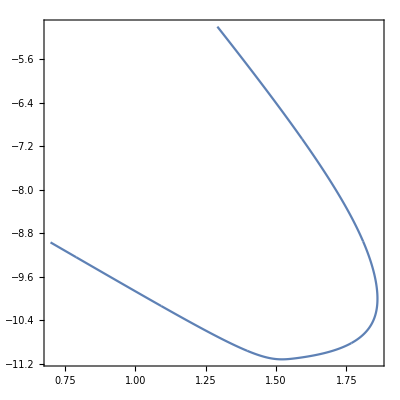

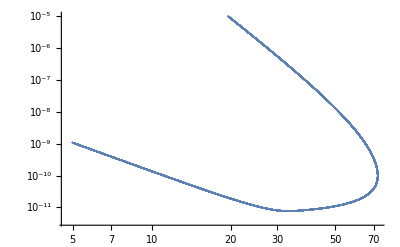

```mathematica
MainDetectorplot1=ContourPlot[{NobsForPlot==Nobs},{m,Log10[Mmin],Log10[Mmax]},{u2,U2min,U2max},PlotRange->All,PerformanceGoal->"Quality",PlotPoints->1000,MaxRecursion->recursionen] 

MainDetectorpointsLog1=MainDetectorplot1[[1,1]];(*all points*)
MainDetectorpoints1=Table[{10^MainDetectorpointsLog1[[i]][[1]],10^MainDetectorpointsLog1[[i]][[2]]},{i,1,Max[Dimensions[MainDetectorpointsLog1]]}];

ListLogLogPlot[MainDetectorpoints1]
```

### Exporting curve data

```mathematica
NumberOfEvents=ToString[Nobs]; (*based on equation (2) *)
NumberOfZ=StringReplace[ToString[NumberForm[Log10[NZ*IP],3]],{"."->"d"}]
lenght=StringReplace[ToString[NumberForm[l/((100)*cm),3]],{"."->"d"}];
diameter=StringReplace[ToString[NumberForm[d/((100)*cm),3]],{"."->"d"}];
efficiency=ToString[ϵαβ];

If[cdec==1&&cprod==1,type="Majorana",
If[cdec==1/2&&cprod==1,type="Dirac",
If[cdec==1&&cprod==2,type="PseudoDirac",type="Other"]
]
];
filename="FCC_HNL_sensitivity_"<>NumberOfEvents<>"events_10e"<>NumberOfZ<>"Z_diameter"<>diameter<>"m_lenght"<>lenght<>"m_efficieny"<>efficiency<>type<>".csv"
```

12d7

FCC_HNL_sensitivity_4events_10e12d7Z_diameter10d0m_lenght8d60m_efficieny1Majorana.csv

```mathematica
SetDirectory[NotebookDirectory[]]
```

C:\Users\drewes\Documents\Mathematica Notebooks\ICHEP

```mathematica
Export[filename,MainDetectorpoints1]
```

FCC_HNL_sensitivity_4events_10e12d7Z_diameter10d0m_lenght8d60m_efficieny1Majorana.csv

### Compare the analytic estimates

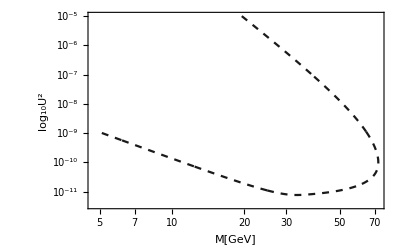

```mathematica
SensitivityRegionPlot=ListLogLogPlot[{MainDetectorpoints1},Frame->True,Joined->True,PlotStyle->{{Dashed,RGBColor[0.1,0.1,0.1]}},FrameLabel->{"M[GeV]","log_10U^2"}]
```

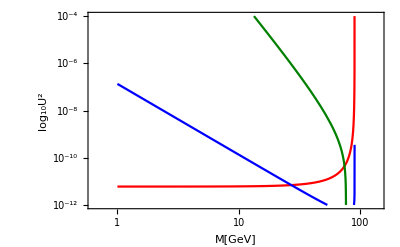

```mathematica
AnalyticPlot1=LogLogPlot[{REDLINE1,GREENLINE1,BLUELINE1},{M,1,90},PlotStyle->{RGBColor[1,0,0],RGBColor[0,0.5,0],RGBColor[0,0,1]},PlotRange->{10^(-12),10^(-4)},Frame->True,FrameLabel->{"M[GeV]","log_10U^2"}]; (*Plots equations (3) and (4) in same colour code as figure 1*)

AnalyticPlot2=LogLogPlot[{REDLINE2,GREENLINE2,BLUELINE2},{M,1,90},PlotStyle->{RGBColor[1,0,0],RGBColor[0,0.5,0],RGBColor[0,0,1]},PlotRange->{10^(-12),10^(-4)},Frame->True,FrameLabel->{"M[GeV]","log_10U^2"}]
```

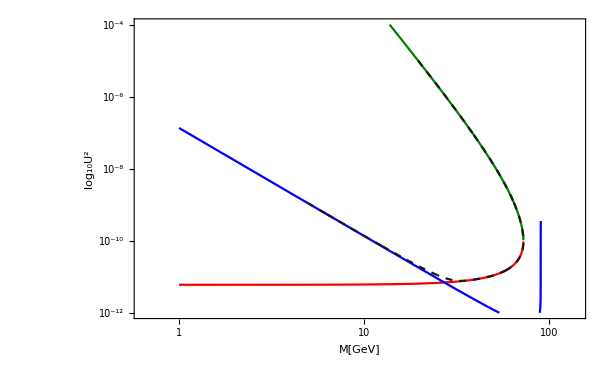

```mathematica
Show[AnalyticPlot1,SensitivityRegionPlot]
```

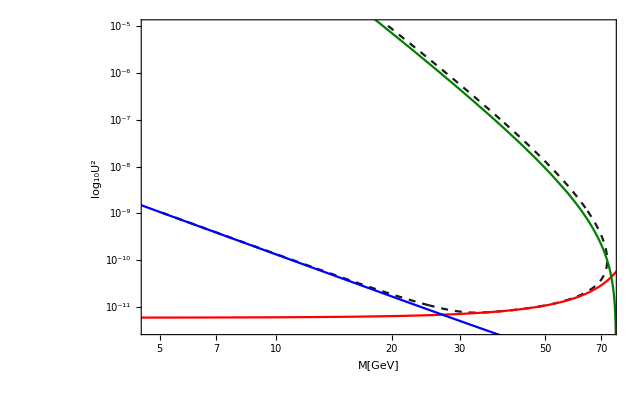

```mathematica
Show[SensitivityRegionPlot,AnalyticPlot2]
```

```mathematica
Mcrit
```

28.1908

### Compare to simulation from 2203.05502 for IDEA and 4 events (only matches if you pick IDEA dimensions, Majorana HNLs 4 events, single flavour mixing, 100% efficiencies)

```mathematica
MaksymCLD4events={{18.32812529555948,0.000013756390840514512},{19.236844875069252,9.979775766300747*^-6},{19.33612657720078,9.654175801423745*^-6},{19.4108798588057,9.41204300297604*^-6},{19.958681250566734,7.824919187836423*^-6},{20.373328359469006,6.826064690675866*^-6},{21.280879918953694,5.1038095131157016*^-6},{21.43856262233907,4.861164487939014*^-6},{21.628949886426593,4.572307351119169*^-6},{22.53124535579844,3.4862623319804256*^-6},{23.317906842687684,2.7676107661146267*^-6},{23.649624529809508,2.516720406039219*^-6},{24.021054897783934,2.2654391918706757*^-6},{24.794284154384798,1.829068319143554*^-6},{25.527800730133038,1.5007749276358914*^-6},{25.96230417946162,1.337274257647106*^-6},{26.413159909141275,1.1873207109788933*^-6},{27.156604655102676,9.843081741846905*^-7},{27.919905741490375,8.138158049524044*^-7},{28.37192949119511,7.284130852996209*^-7},{28.805264920498615,6.562729709918615*^-7},{29.610030717776553,5.421944854650374*^-7},{30.498893956860016,4.4130279110780286*^-7},{30.86798828478429,4.0563807536955643*^-7},{31.197369931855956,3.759885268062238*^-7},{32.148138232268494,3.052025450280064*^-7},{33.272941516417475,2.393024960370816*^-7},{33.445808480128846,2.306663737233923*^-7},{33.5894749432133,2.2274092961261293*^-7},{34.73063050771336,1.7621890800664416*^-7},{34.759831008340285,1.7506420085284785*^-7},{35.00745125365657,1.6649235837116447*^-7},{35.981579954570634,1.3644600462344006*^-7},{36.09429388699055,1.3356158156438632*^-7},{36.23620832003738,1.2976506327055703*^-7},{37.44160498591667,1.0223352620673716*^-7},{38.37368496592798,8.52995340656538*^-8},{38.8058523752064,7.859355583483789*^-8},{39.38869436771974,7.036688678333866*^-8},{40.182947984771985,6.061890898909552*^-8},{40.76578997728532,5.43873595422132*^-8},{41.57172379458834,4.6895059727921685*^-8},{42.71521539913854,3.815741025190613*^-8},{42.973347824680516,3.639767568495929*^-8},{43.15789498864266,3.517861448093427*^-8},{44.17524043048458,2.9413080325975543*^-8},{44.387236065036014,2.833889412287961*^-8},{45.55,2.309662306370962*^-8},{45.80813242554197,2.2103997679823852*^-8},{46.187738933691946,2.069137947818117*^-8},{47.23720492622348,1.7276955475324548*^-8},{47.94210501135734,1.5309859420398358*^-8},{48.67211752703035,1.3524228559741418*^-8},{49.7794005108032,1.1220184543019653*^-8},{50.112286217950086,1.0600877096892432*^-8},{50.334210022714686,1.0209148455507781*^-8},{51.394188195471905,8.555091275879341*^-9},{51.558879019007726,8.323095680469472*^-9},{52.72631503407202,6.840444370698563*^-9},{53.004303800040304,6.532782436268393*^-9},{53.42946308916828,6.08429908272522*^-9},{53.922367539750695,5.5959284575123555*^-9},{54.4514806111105,5.129867794039327*^-9},{55.11842004542936,4.577833486335144*^-9},{55.25916645845111,4.48039012588287*^-9},{55.89515336210545,4.024619345626685*^-9},{57.0725175473829,3.2992946939612663*^-9},{57.33532205302518,3.154671252138302*^-9},{57.510525056786705,3.059965626039524*^-9},{58.386540075594326,2.6368541365780997*^-9},{58.768482623794455,2.46833854938155*^-9},{59.90263006814405,2.026515472977771*^-9},{60.18996299431295,1.925562163156066*^-9},{60.60928218331553,1.7890878356895808*^-9},{61.599763164580665,1.4976576914410289*^-9},{62.294735079501386,1.3182461148061126*^-9},{62.98853897439703,1.158594703588978*^-9},{63.917114894333096,9.70157436882177*^-10},{64.35161834366168,8.904209228577541*^-10},{64.68684009085872,8.330180574152627*^-10},{65.68257716223673,6.787193389424117*^-10},{66.84300505715055,5.260811870508413*^-10},{66.96739918982124,5.112799725244451*^-10},{67.07894510221607,4.979356843896134*^-10},{68.18856412603904,3.7892593282037024*^-10},{69.19656540768035,2.852747449509416*^-10},{69.31920751031342,2.7440493991683494*^-10},{69.47105011357341,2.605014859343056*^-10},{70.30326438144067,1.914000875259002*^-10},{70.71966352038054,1.5469414628385092*^-10},{70.99531624629869,1.238931622394267*^-10},{71.08875784830484,1.0226536581112445*^-10},{71.01517258672499,8.388502423726549*^-11},{70.56957294715818,6.33324577001345*^-11},{70.5059158557915,6.17717224600583*^-11},{69.47105011357341,4.6352282936139246*^-11},{69.43016941269572,4.596606096602571*^-11},{69.37994455161743,4.5487805843505315*^-11},{67.98766468172585,3.605173303851071*^-11},{67.43927927995227,3.349656441577043*^-11},{67.07894510221607,3.2085731535024815*^-11},{66.3647008568816,2.9611882309615315*^-11},{64.83517863404349,2.562050013401664*^-11},{64.68684009085872,2.532364304398745*^-11},{64.61267081926636,2.5138917522903696*^-11},{64.38432290436383,2.4666387108668567*^-11},{62.768951209682584,2.1848159708493066*^-11},{62.294735079501386,2.1154298172901213*^-11},{61.49055329223599,2.0079459164819312*^-11},{60.856318418619274,1.9325919698478585*^-11},{59.90263006814405,1.831659151486747*^-11},{58.886452646327214,1.7347012828355455*^-11},{58.43793295669771,1.695748413578507*^-11},{57.510525056786705,1.6272406284909303*^-11},{56.872786123094755,1.5746207810795036*^-11},{55.52839507423133,1.4854870776777796*^-11},{55.11842004542936,1.464769263022454*^-11},{54.82057493903477,1.4434774307811026*^-11},{52.8080764358274,1.3375686993738824*^-11},{52.73624320428518,1.3341755182488012*^-11},{52.72631503407202,1.3343748786434947*^-11},{52.71463483382125,1.3335776157578763*^-11},{50.62154294888359,1.2427684419840738*^-11},{50.334210022714686,1.2331500829432716*^-11},{49.963947674765336,1.2166785074810094*^-11},{48.48523432301806,1.1640413178186098*^-11},{47.94210501135734,1.1464354736798874*^-11},{47.26406938680025,1.1245500924682127*^-11},{46.326149306663545,1.096673338555639*^-11},{45.55,1.0786349673992337*^-11},{44.60390377968777,1.050012078735995*^-11},{44.14603992985765,1.0387767361918276*^-11},{43.15789498864266,1.0184899189354788*^-11},{41.97819476331506,9.890956558237844*^-12},{41.948994262688146,9.88209340288779*^-12},{40.76578997728532,9.640004001512615*^-12},{39.735596315167555,9.440448208385368*^-12},{39.37701416746897,9.37578573649338*^-12},{38.37368496592798,9.200925913390184*^-12},{37.50701410732097,9.053644001442166*^-12},{36.80153001217457,8.946068381340625*^-12},{35.981579954570634,8.823935671771095*^-12},{35.257991549035545,8.728213546293521*^-12},{34.2645905177077,8.620639680505739*^-12},{33.5894749432133,8.574394341267139*^-12},{32.947063929421034,8.548809767713142*^-12},{31.853797185949134,8.579520436887049*^-12},{31.197369931855956,8.656780647912445*^-12},{30.450421125819325,8.78053469534164*^-12},{29.64390329850378,8.988944386812939*^-12},{28.805264920498615,9.289332193011946*^-12},{27.62673271519609,9.849663062060529*^-12},{27.612716474895173,9.858497130947108*^-12},{27.602204294669484,9.867339123025842*^-12},{26.413159909141275,1.0629559691055836*^-11},{25.714683934145334,1.1186845897282819*^-11},{24.241226672510912,1.2643070705438134*^-11},{24.021054897783934,1.293542603245524*^-11},{23.917101115552093,1.302463846176443*^-11},{23.63677630953366,1.3375686993738824*^-11},{22.205951778814544,1.550341664547042*^-11},{21.628949886426593,1.6586612520624376*^-11},{20.566051663606686,1.8793416573282966*^-11},{20.03810661227196,2.0094465606426002*^-11},{19.236844875069252,2.239014066558643*^-11},{18.99156066980312,2.3166036824114098*^-11},{18.553553160399304,2.4666387108668567*^-11},{17.482478797403857,2.903791465338733*^-11},{16.84473986371191,3.222024700262404*^-11},{16.0388060464089,3.701236077104793*^-11},{14.917506822335149,4.5487805843505315*^-11},{14.655870336717939,4.791557554717178*^-11},{14.45263485235457,4.9932849387598035*^-11},{13.334839688356048,6.302095378554218*^-11},{12.100242521849843,8.388502423726549*^-11},{12.081554201448611,8.433745169143798*^-11},{12.06052984099723,8.509692646196395*^-11},{10.891925805907864,1.147173186038817*^-10},{9.862316153802642,1.5469414628385092*^-10},{9.77471465192188,1.5895853820296842*^-10},{9.66842482963989,1.6461451266913249*^-10},{8.727000689427967,2.2421292456305076*^-10},{8.06356531518433,2.852747449509416*^-10},{7.75053594846374,3.220727688360514*^-10},{7.276319818282548,3.910040255851981*^-10},{6.84882448910443,4.715777331056078*^-10},{6.610548403988757,5.260811870508413*^-10},{6.021866311350037,7.038149606493061*^-10},{5.905064308842354,7.471615162047906*^-10},{5.4331842187113155,9.70157436882177*^-10},{5.26615735512533,1.069745031583257*^-9},{4.884214806925208,1.362298568733622*^-9},{4.584617670493001,1.6570785367492684*^-9},{4.475407798148318,1.7890878356895808*^-9},{4.252899983371183,2.102702128793686*^-9},{3.9719911673402057,2.6125398668029976*^-9},{3.6916663613217677,3.2992946939612663*^-9},{3.42594180561679,4.1896738952287164*^-9},{3.233802511491652,5.0326908420078895*^-9},{3.0469193074793597,6.08429908272522*^-9},{2.9394614651722915,6.822071948644108*^-9},{2.5148861860568648,1.1154992688049985*^-8},{2.5096300959440194,1.1220184543019653*^-8},{2.5084620759189424,1.1267223781277517*^-8},{2.492109795567867,1.1491650263648665*^-8},{2.276610100941192,1.52368335357069*^-8},{2.12651952771882,1.884379213170204*^-8},{2.0616944163270565,2.069137947818117*^-8},{1.9770129645089864,2.360600131250485*^-8},{1.798305900672232,3.195137627798416*^-8},{1.6972721685030865,3.815741025190613*^-8},{1.5740460558574814,4.82598506545819*^-8},{1.5103889644907942,5.473791423434722*^-8},{1.3930029519705731,7.036688678333866*^-8},{1.2960572898891967,8.809736102300859*^-8},{1.2656887692371992,9.481756103630369*^-8},{1.2563446090365846,9.653295041032049*^-8},{1.141294636566517,1.2976506327055703*^-7},{1.0554451647233702,1.656982131454923*^-7},{1.0098923837453744,1.8960448509487753*^-7}};
```

```mathematica
Simulation4eventsIDEA=ListLogLogPlot[MaksymCLD4events,Frame->True,PlotStyle->RGBColor[0,0,0],FrameLabel->{"M[GeV]","log_10U^2"}];
```

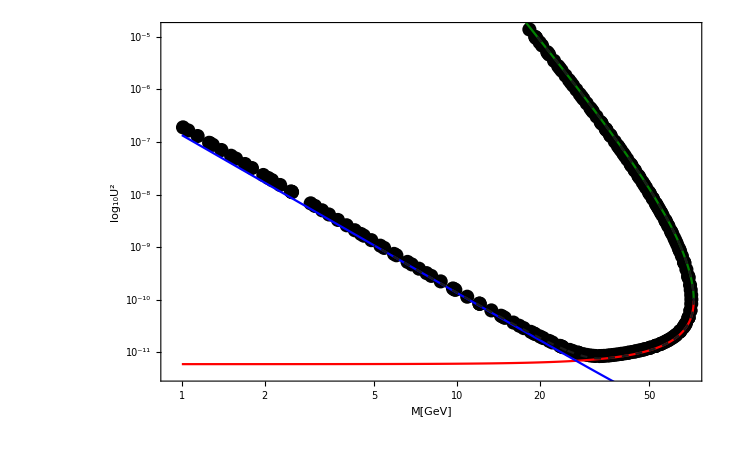

```mathematica
Show[Simulation4eventsIDEA,AnalyticPlot1,SensitivityRegionPlot]
```